# Подкаст 2 : “Числа Фибоначчи”

## Рекурсивное определение

{1, 1, 2, 3, 5, 8, 13, ...}

```mathematica
F[n_]:=F[n-1] + F[n-2];
```

```mathematica
F[3]
```

```mathematica
F1[n_]:=If[n==0 || n==1, 1, F1[n-1] + F1[n-2]];
```

```mathematica
F1[20]
```

```mathematica
Range[0,20]
```

```mathematica
F1/@Range[0,20]
```

```mathematica
F[n_]:=F[n-1] + F[n-2];
F[0]=1;
F[1]=1;
```

```mathematica
F[20]
```

```mathematica
F/@Range[0,20]
```

```mathematica
F/@Range[25]//Timing
```

```mathematica
F1/@Range[25]//Timing
```

## Рекурсия с запоминанием (recursion & memoization)

```mathematica
F2[n_]:=(F2[n]=F2[n-1] + F2[n-2]);
F2[0]=1;
F2[1]=1;
```

```mathematica
F2/@Range[35]//Timing
```

```mathematica
g[n_]:=n;
g[n_, a_]:=n + a;
g[42]=1;
g[13]=b;
g[b]=3;
g[n_,3]:=100;
g[3,a_]:=200;
```

```mathematica
{g[5], g[42], g[5,1]}
```

```mathematica
{g[5,3], g[3,5],g[3,3]}
```

```mathematica
g[b]
```

```mathematica
b=2
```

```mathematica
g[b]
```

```mathematica
g[n1,a1]
```

```mathematica
g[a]
```

```mathematica
Definition[g]
```

```mathematica
FullDefinition[g]
```

```mathematica
ShowViewerStatus[]
```

## Цепная дробь 1/(1+1/(1+1/(1+1/(1+1/(...)))))

```mathematica
1/(1+1)
```

```mathematica
1/(1+1/(1+1))
```

```mathematica
1/(1+1/(1+1/(1+1)))
```

```mathematica
1/(1+1/(1+1/(1+1/(1+1))))
```

```mathematica
FibCF[n_]:=If[n==0,1,1/(1+ FibCF[n-1])];
```

```mathematica
FibCF[6]
```

```mathematica
FibCF/@Range[20]
```

```mathematica
Numerator[FibCF/@Range[20]]
```

```mathematica
Numerator[FibCF/@Range[20]]//Timing
```

```mathematica
F2/@Range[20]//Timing
```

## Разбиение прямоугольника на квадраты

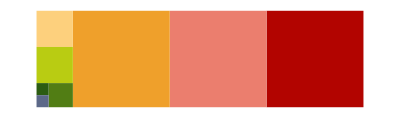

```mathematica
SplitToSquares[{{x1_,y1_},{x2_,y2_}}, n_]:=Module[
{a,b},
If[
n==0,
(* Stop recursion *) 
{{{x1,y1},{x2,y2}}},
(* Take one square and continue recursion *)
a=x2-x1;
b=y2-y1;
If[
a<b,
Prepend[ SplitToSquares[{{x1,y1},{x2,y2-a}}, n-1], {{x1,y2-a},{x2,y2}}],
Prepend[ SplitToSquares[{{x1,y1},{x2-b,y2}}, n-1], {{x2-b,y1},{x2,y2}}]
]
]
]
```

```mathematica
SplitToSquares[{{0,0},{13,8}}, 5]
```

```mathematica
Rectangle[{0,8},{8,8}]
```

```mathematica
Graphics[{Hue[0.79,0.7,0.5],Rectangle[{0,0},{8,8}]}]
```

```mathematica
colors=ColorData[10,"ColorList"]
```

```mathematica
sqs=SplitToSquares[{{0,0},{27,8}}, 8];
sqsG=(
i=#;
{colors⟦i⟧,Rectangle[sqs⟦i,1⟧, sqs⟦i,2⟧]}
)&/@Range[Length[sqs]];

gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
n=12;
sqs=SplitToSquares[{{0,0},{F[n],F[n-1]}}, n-1];
Co[i_]:=colors⟦1+Mod[i+1,Length[colors]]⟧
sqsG=(
i=#;
{Co[i],Rectangle[sqs⟦i,1⟧, sqs⟦i,2⟧]}
)&/@Range[Length[sqs]];

gs=Flatten[sqsG];
Graphics[gs]
```

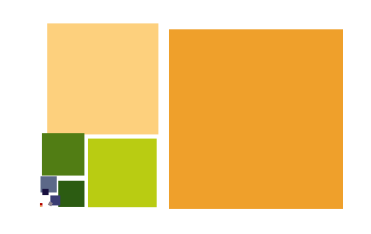

### Формула суммы квадратов чисел Фибоначчи

```mathematica
F[0]^2+F[1]^2+F[2]^2+F[3]^2+F[4]^2
```

```mathematica
F[4]*F[5]
```

```mathematica
F/@Range[0,15]
```

```mathematica
(F/@Range[0,15])^2
```

```mathematica
Clear[a,b,c,d];Accumulate[{a,b,c,d,e}]
```

```mathematica
Accumulate[(F/@Range[0,15])^2]
```

```mathematica
(F/@Range[0,15])
```

```mathematica
(F/@Range[1,16])
```

```mathematica
(F/@Range[0,15]) * (F/@Range[1,16])
```

Мы доказали, что 
F[0]^2+F[1]^2+F[2]^2+F[3]^2+.. +F[n]^2 == F[n] F[n+1]

```mathematica
ShowViewerStatus[]
```

## Анализ ряда {1, 1, 2, 3, 5, 8, 13, ...} и явная формула

```mathematica
SetOptions[{Plot,ListPlot},GridLines->Automatic];
```

```mathematica
F=F2;
```

```mathematica
fibs=F/@Range[1000];
```

```mathematica
Take[fibs,100]
```

```mathematica
ListPlot[Take[fibs,100]]
```

```mathematica
{Log[2,2],Log[2,4],Log[2,8],Log[2,16]}
```

```mathematica
N[E]
```

```mathematica
Log[E,n]==Log[n]
```

```mathematica
N[Log[16]]
```

```mathematica
ListPlot[Log[Take[fibs,10]]]
```

```mathematica
fit=Fit[Log[Take[fibs,200]],{1,x},x]
```

```mathematica
N[F[100]/F[99]]
```

```mathematica
phi=(Sqrt[5]+1)/2
```

```mathematica
N[phi,30]
```

```mathematica
Show[ListPlot[Log[Take[fibs,10]]],Plot[fit, {x,0,10}]  ]
```

```mathematica
g1=ListPlot[Log[Take[fibs,10]]];
g2=Plot[fit, {x,0,10},PlotStyle->ColorData["Rainbow"]];
Show[g1,g2]
```

```mathematica
fit
```

```mathematica
ListPlot[Log[Take[fibs,1000]] - (fit/.{x->Range[1000]})]
```

```mathematica
ListPlot[Log[Take[fibs,100]] - (Log[phi] * Range[100])]
```

```mathematica
{a,b,c,d}- {1,2,3,4}
```

```mathematica
ListPlot[Log[Take[fibs,100]] - (Log[phi] * Range[100])+0.32350713]
```

```mathematica
FibApprox[n_]:=phi^n*Exp[-0.32350713]
```

```mathematica
FibApprox[Range[10]]
```

```mathematica
Round[FibApprox[Range[20]]]
```

```mathematica
SetAttributes[F2,Listable]
```

```mathematica
F=F2;
```

```mathematica
F[Range[20]]
```

```mathematica
Table[(FibApprox[n]-F[n]),{n,1,20}]
```

```mathematica
c[n_]:=λ^n;
c[m]==c[m-1]+c[m-2]
```

```mathematica
c[m]/λ^m==(c[m-1]+c[m-2])/λ^m
```

```mathematica
Simplify[c[m]/λ^m==(c[m-1]+c[m-2])/λ^m]
```

```mathematica
Solve[λ==1+1/λ,λ]
```

```mathematica
-1/phi==1/2 (1-√5)
```

```mathematica
N[Solve[λ==1+1/λ,λ]]
```

```mathematica
(c[n]==c[n-1]+c[n-2])/.{λ->1/2 (1-√5)}
```

```mathematica
FullSimplify[(c[n]==c[n-1]+c[n-2])/.{λ->1/2 (1-√5)}]
```

```mathematica
FullSimplify[(c[n]==c[n-1]+c[n-2])/.{λ->1/2 (1+√5)}]
```

```mathematica
c[n_,{a_,b_}]:=a phi^n + b (-1/phi)^n;
```

```mathematica
a λ1^n == a λ1^(n-1) + a λ1^(n-2);
b λ2^n  == b λ2^(n-1)  + b λ2^(n-2) ;
(a λ1^n + b λ2^n) == (a λ1^(n-1) + b λ2^(n-1) ) + (a λ1^(n-2) + b λ2^(n-2) );
```

```mathematica
ClearAll[a,b];
```

a = ? ; b = ?

```mathematica
Solve[
{
a phi^0 + b (-1/phi)^0==1,
a phi^1 + b (-1/phi)^1==1
},
{a,b}
]
```

```mathematica
F3[n_]:=(3+√5)/(5+√5)phi^n+(2/(5+√5))(-1/phi)^n;
```

```mathematica
Expand[(3+√5)(5-√5)]/Expand[(5+√5)(5 -√5)]
```

```mathematica
1/20 (10+2 √5)==1/2(1+1/(√5))
```

```mathematica
(Expand[2 (5-√5)]/Expand[(5+√5) (5-√5)])
```

```mathematica
(2/(5+√5))==1/2(1-1/(√5))
```

```mathematica
F3[n_]:=1/2(1+1/(√5))phi^n+1/2(1-1/(√5))(-1/phi)^n;
```

```mathematica
F3[Range[10]]
```

```mathematica
N[F3[Range[10]]]
```

```mathematica
FullSimplify[F3[Range[10]]]
```

```mathematica
(F3[Range[25]];)//Timing
```

## Производящая функция

```mathematica
F[Range[0,10]]
```

```mathematica
x^Range[0,10]
```

```mathematica
g10 = Plus@@(x^Range[0,10] * F2[Range[0,10]])
```

```mathematica
g10 + x g10
```

```mathematica
Expand[g10 + x g10]
```

```mathematica
g10 + x g10 == (g10)/x
```

```mathematica
g10/x
```

```mathematica
Simplify[(g10-1)/x]
```

```mathematica
g10 + x g10 ==( g10-1)/x
```

```mathematica
g + x g == ( g-1)/x;
```

```mathematica
Solve[ g + x g == ( g-1)/x,g]
```

```mathematica
G[x_]:=1/(1-x -x^2);
```

(* В школе рассказывают, что *)
1/(1-q)=1+q+q^2+q^3+q^4...
(* Это называется разложение функции в степенной ряд.  *)

```mathematica
(* Разложение в степенной ряд любой функции можно получить с момощью функции Series*)
Series[1/(1-x),{x,0,10}]
```

```mathematica
(* умножим обе части 1/(1-x)=1+x+x^2+x^3+x^4... на (1 - x) *)
Expand[(1 - x)(1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10)]
```

```mathematica
G[x_]:=1/(1-x -x^2);
```

```mathematica
Series[G[x],{x,0,10}]
```

### Числа фибоначчи как суммы "диагоналей" чисел в треугольнике Паскаля

1/(1-q)==1+q+q^2+q^3+...;
q == x + x^2;

1/(1-x -x^2)=1 + (x+x^2)+(x+x^2)^2+(x+x^2)^3+(x+x^2)^4+(x+x^2)^5+(x+x^2)^6+(x+x^2)^7+...

```mathematica
Grid[Table[{Expand[(x+y)^n]},{n,1,6}]]
```

```mathematica
Binomial[6,Range[0,6]]
```

```mathematica
Expand[(x+y)^6]
```

```mathematica
{F[6],F[6]==1+5+6+1}
```

```mathematica
Binomial[6,0]+ Binomial[5,1]+ Binomial[4,2]+ Binomial[3,3]
```

```mathematica
Binomial[7,0]+ Binomial[6,1]+ Binomial[5,2]+ Binomial[4,3]
```

```mathematica
F[6]
```

```mathematica
(* Мы доказали *)
F[n] == Binomial[n,0] + Binomial[n-1,1]  + Binomial[n-2,2] + ...;
```

```mathematica
Series[1/(1-x -x^2),{x,0,10}]
```

```mathematica
Series[1/(1+x -x^2),{x,0,10}]
```

```mathematica
(1-x -x^2)(1+x-x^2) == ((1-x^2) -x )((1-x^2) + x) == (1-x^2)^2 - x^2 =-1+(1-x^2) +(1-x^2)^2
```

```mathematica
Series[1/(1-x -x^2) 1/(1+x -x^2),{x,0,10}]
```

```mathematica
Ga[x_,n_]:=Plus@@(Table[a[m] x^m,{m,0,10}])
Gb[x_,n_]:=Plus@@(Table[b[m] x^m,{m,0,10}])
```

```mathematica
{Ga[x,10],Gb[x,10]}
```

```mathematica
x^6(a[0] * b[6] + a[1] * b[5]+a[2] * b[4]+... + a[6]*b[0])
```

```mathematica
F[0]F[6] -F[1]F[5]+F[2]F[4]-F[3]F[3]+F[4]F[2]-F[5]F[1]+F[6]F[1]
```

```mathematica
F[0]F[5] -F[1]F[4]+F[2]F[3]-F[3]F[2]+F[4]F[1]-F[5]F[0]
```

```mathematica
ConFm[n_]:=Plus@@Table[F[n-k]*F[k]*(-1)^k,{k,0,n}]
```

```mathematica
ConFm/@Range[15]
```

```mathematica
{ConFm[10],F[11]}
```

```mathematica
{ConFm[12],F[13]}
```

```mathematica
(* Мы доказали, что для n = 2m + 1 *)
n=15;
ConFm[n-1]==F[n]
```

```mathematica
Collect[Expand[Ga[x,10]*Gb[1x,10]],x]
```

### Наблюдение про производную

```mathematica
Definition[G]
```

```mathematica
G'[x]
```

```mathematica
ShowViewerStatus[]
```

```mathematica
{G'[x], G[x]^2}
```

```mathematica
G'[x]-(2x +1)G[x]^2
```

```mathematica
Together[G'[x]-(2x +1)G[x]^2]
```

```mathematica
G'[x] == (1+2x)G[x]^2
```

```mathematica
Series[G[x]^2,{x,0,10}]
```

```mathematica
Series[(1+2x)G[x]^2,{x,0,10}]
```

```mathematica
Series[G'[x],{x,0,10}]
```

```mathematica
F[0]F[5] + F[1]F[4] + F[2]F[3]+F[3]F[2] + F[4]F[1] + F[5]F[0]
```

```mathematica
F[0]F[6] + F[1]F[5] + F[2]F[4]+F[3]F[3] + F[4]F[2]+ F[5]F[1]+F[6]F2[0]
```

```mathematica
ConF[n_]:=Plus@@Table[F[n-k]*F[k],{k,0,n}]
```

```mathematica
SetAttributes[ConF,Listable];
```

```mathematica
ConF[{5,6}]
```

```mathematica
F[11] * 11
```

```mathematica
ConF[10] + 2 ConF[9]
```

```mathematica
(* Мы доказали, что *)
n=15;
ConF[n-1] + 2 ConF[n-2] == F[n] n
```

```mathematica
TableForm[{Range[1,10] , F[Range[1,10]]}]

Range[1,10] * F[Range[1,10]]
```

```mathematica
ConF[Range[1,10]]+ 2ConF[Range[0,9]]
```

### Интересные наблюдения “на подумать”

```mathematica
Series[G[x],{x,1,10}]
```

```mathematica
Series[G[x],{x,-1,10}]
```

```mathematica
Plot[1/G[x],{x,-5,5}]
```

```mathematica
ComplexPlot[G[z],{z,-5-5I,5+5I},ColorFunction->"CyclicLogAbsArg"]
```

```mathematica
ComplexPlot[1/((z-1)(z+1)),{z,-5-5I,5+5I},ColorFunction->"CyclicLogAbsArg"]
```

```mathematica
ComplexPlot[1/z,{z,-5-10I,5+10I},ColorFunction->"CyclicLogAbsArg"]
```

## Бонус трек 1: Числа Фибоначчи и Матрицы

Вспомним как мы получили явную формулу для чисел Фибоначчи :

```mathematica
F[n_]:=(F[n]=F[n-1] + F[n-2]);
F[0]=1;
F[1]=1;
```

```mathematica
SetAttributes[F,Listable]
```

```mathematica
F[Range[20]]
```

```mathematica
ff[n_]:=λ^n;
```

```mathematica
ff[n]==ff[n-1] + ff[n-2]
```

```mathematica
Clear[n];
Solve[ff[n]==ff[n-1] + ff[n-2],λ]
```

```mathematica
phi=1/2 (1+√5);
```

```mathematica
-1/phi == 1/2 (1-√5)
```

```mathematica
Clear[a,b];
Solve[
{
a phi^0 + b (-1/phi)^0==1,
a phi^1 + b (-1/phi)^1==1
},
{a,b}
]
```

```mathematica
F3[n_]:=(3+√5)/(5+√5)phi^n+(2/(5+√5))(-1/phi)^n;
```

```mathematica
Expand[(3+√5)(5-√5)]/Expand[(5+√5)(5 -√5)]
```

```mathematica
1/20 (10+2 √5)==1/2(1+1/(√5))
```

```mathematica
(Expand[2 (5-√5)]/Expand[(5+√5) (5-√5)])
```

```mathematica
(2/(5+√5))==1/2(1-1/(√5))
```

```mathematica
F3[n_]:=1/2(1+1/(√5))phi^n+1/2(1-1/(√5))(-1/phi)^n;
```

```mathematica
Simplify[F3/@Range[10]]
```

Числа Фибоначчи – “почти геометрическая прогрессия”. Как мы показали выше – это сумма двух геометрический прогрессий.
 Но в векторном пространстве это и есть геометрическая прогрессия. Эта фраза, конечно, требует пояснения

```mathematica
(* Пример обычной геометрической прогрессии (какой-то): *)
b0=3;  q=2;
{b0, q * b0,  q * q * b0, q * q * q * b0, q * q * q * q * b0,  q * q * q * q * q * b0}
```

Забегая вперед : b – не число, а вектор, q – не число, а матрица, 
вместо умножения чисел – матричное умножение (вместо символа звездочки * символ точки .)

```mathematica
b0= ({{1}, {1}});  q = ({{1, 1}, {1, 0}});
{(q . q). b0, (q . q). b0 ,(q . q . q). b0, (q . q . q . q). b0,(q . q . q . q . q). b0}
```

```mathematica
(* Пара соседних чисел зависит от предыдущей пары соседних по правилу: *)
{F[n],F[n-1]} == {F[n-1] + F[n-2], F[n-1]}
```

```mathematica
(* Пусть {x, y} =  {F[n], F[n-1]}. 
Запишем общую идею как из пары чисел {x, y} сделать новую пару.   *)
Clear[a,b,c,d];
NewPoint[{x_,y_},{a_,b_,c_,d_}]:={a x + b y, c x + d y};
```

```mathematica
NewPoint[{x,y},{a,b,c,d}]
```

```mathematica
(* новая пара {x,y} = {F[n], F[n-1]}. Старая пара {x,y} = {F[n-1], F[n-2]}*)
{F[n],F[n-1]} == {a F[n-1] +  b F[n-2], c F[n-1] + d F[n-1]};
a == 1; b == 1; c == 1; d == 0;
```

```mathematica
NewPoint[{x,y},{a,b,c,d}]
```

```mathematica
NewPointList[l_,{a_,b_,c_,d_}]:=NewPoint[#, {a,b,c,d}]&/@l;
```

```mathematica
NewPointList[{{x,y}, {u,v}},{a,b,c,d}]
```

```mathematica
(* А как сделать функцию NewPoint, работающую как для пары {x, y}, так и для списка пар? Вот так: *)
NewPoint[
{x_?(!ListQ[#]&),y_?(!ListQ[#]&)},{a_,b_,c_,d_}
]:={a x + b y, c x + d y};
NewPoint[
l_?MatrixQ,{a_,b_,c_,d_}
]:=NewPoint[#, {a,b,c,d}]&/@l;
```

```mathematica
Clear[a,b,c,d];
NewPoint[{x,y},{a,b,c,d}]
NewPoint[{{x,y}, {u,v}},{a,b,c,d}]
```

```mathematica
Flatten[{{1,2},{3,4},{{7,{3}}}}]
```

```mathematica
Flatten[{{1,2},{3,4},{{7,{3}}}},1]
```

```mathematica
Flatten[{{1,2},{3,4},{{7,{3}}}},2]
```

```mathematica
Grid[Table[{5i,j},{i,-5,5},{j,-5,5}],Frame->All]
```

```mathematica
Flatten[Table[{5i,j},{i,-5,5},{j,-5,5}],1]
```

```mathematica
listsOfPoints = {
Flatten[Table[{5i,j},{i,-7,7},{j,-30,30}],1],
Flatten[Table[{i,5j},{j,-7,7},{i,-30,30}],1],
Flatten[Table[2i {Cos[j 2Pi/20 ], Sin[j 2Pi/20 ]},{i,1,20,0.25},{j,-10,10}],1]
};
```

```mathematica
g0=ListPlot[listsOfPoints,AspectRatio->1,PlotStyle->PointSize[0.01],PlotRange->{{-21,21},{-21,21}}]
```

```mathematica
{a,b,c,d}={1,1,0,1};
g1=ListPlot[NewPoint[#,{a,b,c,d}]&/@listsOfPoints,AspectRatio->1,PlotStyle->PointSize[0.01], PlotRange->{{-21,21},{-21,21}}]
```

```mathematica
Manipulate[
gT=ListPlot[NewPoint[#,{at,bt,ct,dt}]&/@listsOfPoints,AspectRatio->1,PlotStyle->PointSize[0.01], PlotRange->{{-21,21},{-21,21}}];
Show[gT],
{{at,1},-2,2},
{{bt,0},-2,2},
{{ct,0},-2,2},
{{dt,1},-2,2}
]
```

```mathematica
t[p_]:=NewPoint[p,{1,1,1,0}]
```

```mathematica
t[t[t[t[{1,1}]]]]
```

```mathematica
t[t[t[{1,1}]]]
```

```mathematica
Nest[h,x,5]
```

```mathematica
NestList[h,x,5]
```

```mathematica
NestList[t,{1,1},5]
```

```mathematica
NestList[t,{1,1},20]
```

```mathematica
ListPlot[NestList[t,{0,1},10],AspectRatio->1,PlotStyle->PointSize[0.03]]
```

```mathematica
ListPlot[Log[NestList[t,{1,1},20]]]
```

```mathematica
Manipulate[
Block[
{t},
t[p_]:=NewPoint[p,{a,b,c,d}];
ListPlot[NestList[t,{1,1},n],Joined->True]
],
{{n,17},3,70,1},
{{a,0.5},-2,2},
{{b,-0.38},-2,2},
{{c,0.85},-2,2},
{{d,0.69},-2,2}
]
```

```mathematica
ShowViewerStatus[]
```

```mathematica
Clear[a,b,c,d];
NewPoint[{x,y},{a,b,c,d}]
```

```mathematica
NewPoint[NewPoint[{x,y},{a,b,c,d}],{a,b,c,d}]
```

```mathematica
t1[p_]:=NewPoint[p,{a1,b1,c1,d1}]
```

```mathematica
t2[p_]:=NewPoint[p,{a2,b2,c2,d2}]
```

```mathematica
t2[t1[{x,y}]]
```

```mathematica
Collect[Expand[t2[t1[{x,y}]]],{x,y}]
```

```mathematica
{a,b,c,d}={(a1 a2+b2 c1), (a2 b1+b2 d1),(a1 c2+c1 d2), (b1 c2+d1 d2)};
```

```mathematica
MatrixForm[{{a,b},{c,d}}]
```

```mathematica
MatrixForm[{{a1,b1},{c1,d1}}]
```

```mathematica
r=({{a2, b2}, {c2, d2}}). ({{a1, b1}, {c1, d1}})
```

```mathematica
MatrixForm[r]
```

```mathematica
({{1, 1}, {1, 0}}).({{1, 1}, {1, 0}})
```

```mathematica
({{1, 1}, {1, 0}}).({{1, 1}, {1, 0}}).({{1, 1}, {1, 0}}).({{1, 1}, {1, 0}}).({{1, 1}, {1, 0}}).({{1, 1}, {1, 0}})
```

```mathematica
MatrixPower[({{1, 1}, {1, 0}}),6]
```

```mathematica
F4[n_]:=MatrixPower[({{1, 1}, {1, 0}}),n]⟦1,1⟧
```

```mathematica
F4/@Range[20]
```

```mathematica
F4/@Range[20]//Timing
```

```mathematica
MatrixPower2[m_,n_]:=If[n==0,{{1,0},{0,1}},m . MatrixPower2[m,n-1]]
```

```mathematica
MatrixPower2[({{1, 1}, {1, 0}}),10]
```

```mathematica
MatrixPower2[({{1, 1}, {1, 0}}),10]//Timing
```

```mathematica
MatrixPower2[({{1, 1}, {1, 0}}),1000]//Timing
```

```mathematica
MatrixPower2o[m_,n_]:=If[
n==0,
{{1,0},{0,1}},
If[
Mod[n,2]==0,
 MatrixPower2o[m . m,n/2],
m . MatrixPower2o[m,n-1]
]
]
```

```mathematica
MatrixPower2o[({{1, 1}, {1, 0}}),10]//Timing
```

```mathematica
MatrixPower2o[({{1, 1}, {1, 0}}),100]//Timing
```

```mathematica
MatrixPower2o[({{1, 1}, {1, 0}}),1000]//Timing
```

```mathematica
MatrixPower2[({{1, 1}, {1, 0}}),1000]//Timing
```

```mathematica
MatrixPower2o[({{1, 1}, {1, 0}}),10000]//Timing
```

```mathematica
Mod[MatrixPower2o[({{1, 1}, {1, 0}}),10005],1597]//Timing
```

```mathematica
Mod[MatrixPower[({{1, 1}, {1, 0}}),10005],1597]//Timing
```

кстати, почему мы здесь снова видим числа Фибоначчи?

## Бонус трек 2: Разбиение прямоугольника на квадраты Комплексные числа. Инверсия

Хочется больше красивых картинок

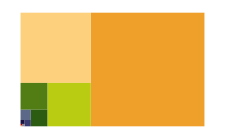
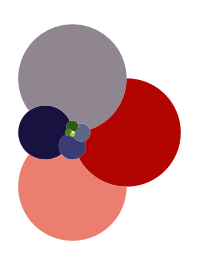
```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
Clear[a,b,c,d, a1,b1,c1,d1,a2,b2,c2,d2]
```

```mathematica
I^2
```

```mathematica
-2 + 3 I
```

```mathematica
(a1+I b1)*(a2+I b2)
```

```mathematica
Expand[(a1+I b1)*(a2+I b2)]
```

```mathematica
ComplexExpand[(a1+I b1)*(a2+I b2)]
```

```mathematica
1/I
```

```mathematica
(I+1)^2 - 2(I+1)
```

```mathematica
(I+1)^2 - 2(I+1)+2
```

```mathematica
Solve[x^2-2x +2 ==0, x]
```

```mathematica
1/(1 + I)
```

```mathematica
(1/2-ⅈ/2)(1+ⅈ)
```

```mathematica
SplitToSquares[{{x1_,y1_},{x2_,y2_}}, n_]:=Module[
{a,b},
If[
n==0,
{{{x1,y1},{x2,y2}}},
a=x2-x1;
b=y2-y1;
If[
a<b,
Prepend[ SplitToSquares[{{x1,y1},{x2,y2-a}}, n-1], {{x1,y2-a},{x2,y2}}],
Prepend[ SplitToSquares[{{x1,y1},{x2-b,y2}}, n-1], {{x2-b,y1},{x2,y2}}]
]
]
]
```

```mathematica
colors=ColorData[10,"ColorList"]
```

```mathematica
Co[i_]:=colors⟦1+Mod[i-1,Length[colors]]⟧;
```

```mathematica
ToPolygon[{{x1_,y1_},{x2_,y2_}}]:={{x1,y1},{x1,y2},{x2,y2},{x2,y1}};
```

```mathematica
sqs=SplitToSquares[{{0,0},{F[10],F[9]}}, 10];
sqsG=(
i=#;
p=ToPolygon[sqs⟦i⟧];
{Co[i],Polygon[p]}
)&/@Range[Length[sqs]];

gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
ToZ[{a_,b_}]:=a+I b;
FromZ[z_]:={Re[z], Im[z]};
```

```mathematica
ToZ[{2,3}]
```

```mathematica
FromZ[2+3 ⅈ]
```

```mathematica
PointT[f_,p_]:=FromZ[f[ToZ[(p)]]];
```

```mathematica
PointT[#^2&,{aa,bb}]
```

```mathematica
Range[0,1,1/7]
```

```mathematica
PointsBetween[p1_,p2_,n_]:=(p2 * # + p1 * (1-#))&/@Range[0,1,1/n];
```

```mathematica
PointsBetween[{x1,y1},{x2,y2},10]
```

```mathematica
2{a,b}+3{c,d}
```

```mathematica
Flatten[{{1,2},{3,4},{{7,{3}}}}]
```

```mathematica
Flatten[{{1,2},{3,4},{{7,{3}}}},1]
```

```mathematica
Flatten[{{1,2},{3,4},{{7,{3}}}},2]
```

```mathematica
ToDetailedPolygon[{{x1_,y1_},{x2_,y2_}}]:=Flatten[
{
PointsBetween[{x1,y1},{x1,y2},100],
PointsBetween[{x1,y2},{x2,y2},100],
PointsBetween[{x2,y2},{x2,y1},100],
PointsBetween[{x2,y1},{x1,y1},100]
},
1
];
```

```mathematica
n=21;
p0={F[n],F[n-1]};
sqs=SplitToSquares[{{0,0},p0}, n+1];
f[z_]:=z^(1/5);
sqsG=(
i=#;
p=PointT[f,#]&/@ToDetailedPolygon[sqs⟦i⟧];
{Co[i],Polygon[p]}
)&/@Range[Length[sqs]];

gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
n=12;
p0={F[n],F[n-1]};
sqs=SplitToSquares[{{0,0},p0}, 10];
f[z_]:=Sqrt[z];
sqsG=(
i=#;
p=PointT[f,#]&/@ToDetailedPolygon[sqs⟦i⟧];
{Co[i],Polygon[p]}
)&/@Range[Length[sqs]];

gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
f[z_]:=If[z==0,ComplexInfinity,1/z];
sqsG=(
i=#;
p=PointT[f,#]&/@ToDetailedPolygon[sqs⟦i⟧];
{colors⟦i⟧,Polygon[p]}
)&/@Range[Length[sqs]];

gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
Intersection[{10,2,3,4},{3,9,10}]
```

```mathematica
Length[Intersection[ToPolygon[sqs⟦12⟧],{pC}]]
```

```mathematica
f[z_]:=If[z==0,ComplexInfinity,1/z];
pC={0,0};
sqsG=(
i=#;
poly=ToDetailedPolygon[sqs⟦i⟧];
If[
Length[Intersection[poly,{pC}]]>0,
{},
p=PointT[(f[#]&),#]&/@poly;
{Co[i],Polygon[p]}
]
)&/@Range[Length[sqs]];
gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
SplitToSquares2[{{x1_,y1_},{x2_,y2_}}, n_,k_]:=Module[
{a,b},
If[
n==1,
{{{x1,y1},{x2,y2}}},
a=x2-x1;
b=y2-y1;
If[
a<b,
If[
Mod[n-k,4]==3,
Prepend[ SplitToSquares2[{{x1,y1},{x2,y2-a}}, n-1,k], {{x1,y2-a},{x2,y2}}],
Prepend[ SplitToSquares2[{{x1,y1+a},{x2,y2}}, n-1,k], {{x1,y1},{x2,y1+a}}]
],
If[
Mod[n-k,4]==0,
Prepend[ SplitToSquares2[{{x1,y1},{x2-b,y2}}, n-1,k], {{x2-b,y1},{x2,y2}}],
Prepend[ SplitToSquares2[{{x1+b,y1},{x2,y2}}, n-1,k], {{x1,y1},{x1+b,y2}}]
]
]
]
]
```

```mathematica
n=8;
p0={F[n],F[n-1]};
sqs=SplitToSquares2[{{0,0},p0}, n, n];
pC=sqs⟦-1,1⟧;
f[z_]:=z;
f2[z_]:=1/(z-ToZ[pC]);
sqsG=(
i=#;
p=(PointT[f,#]&/@ToDetailedPolygon[sqs⟦i⟧]);
{colors⟦1+Mod[i-1,Length[colors]]⟧,Polygon[p]}
)&/@Range[Length[sqs]];
gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
n=35;
N[SplitToSquares2[{{0,0},{F[n],F[n-1]}}, n,n] [[-1]]/F[n],30]
```

Задача : что это за точка, к которой сходится спираль квадратов?

```mathematica
z0=0.27639314 + I 0.170820;
```

```mathematica
Range[17]⟦-1⟧
```

```mathematica
n=17;
p0={F[n],F[n-1]};
sqs=SplitToSquares2[{{0,0},p0}, n,n];
pC=sqs⟦-1,1⟧;
zC=ToZ[pC];
f[z_]:=If[z-zC==0,ComplexInfinity,1/(z-zC)];
sqsG=(
i=#;
poly = ToDetailedPolygon[sqs⟦i⟧];
If[
Length[Intersection[poly,{pC}]]>0,
{},
p=PointT[(f[#]&),#]&/@poly;
{Co[i],Polygon[p]}
]
)&/@Range[Length[sqs]];
gs=Flatten[sqsG];
Graphics[gs]
```

```mathematica
ShowViewerStatus[]
```

```mathematica
fc[z_,zC_]:=If[z-zC==0,ComplexInfinity,1/(z-zC)];
Manipulate[
Block[
{sqs,i,p,p0,zC,pC,sqsG, gs, poly},
p0={F[n],F[n-1]};
sqs=SplitToSquares2[{{0,0},p0}, n,n];
pC=sqs⟦-1,1⟧;
zC=ToZ[pC];
sqsG=(
i=#;
poly=ToDetailedPolygon[sqs⟦i⟧];
If[
Length[Intersection[poly,{pC}]]>0,
{},
p=PointT[(fc[#,zC]&),#]&/@ToDetailedPolygon[sqs⟦i⟧];
{Co[i],Polygon[p]}
]
)&/@Range[Length[sqs]];
gs=Flatten[sqsG];

Graphics[gs]
],
{{n,13},2,20,1}
]
```

## ShowViewerStatus

```mathematica
ShowViewerStatus[]:=-Graphics-;
```

```mathematica
ShowViewerStatus[]:=-Graphics-;
```

```mathematica
boyArr={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
boy=Animate[boyArr[[i]],{i,1,23,1}];
```

```mathematica
girlArr={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
girl=Animate[girlArr[[i]],{i,1,Length[girlArr],1}];
```

```mathematica
ShowViewerStatus[]:=girl;
```

```mathematica
ShowViewerStatus[]:=boy;
```

```mathematica
илюшаArr={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
илюша=Animate[илюшаArr[[i]],{i,1,Length[илюшаArr],1}];
```

```mathematica
ShowViewerStatus[]:=-Graphics-
```